```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->1,cj->U/5,U->6,t23->x t22,t22->0.3}
```

{Δ→1,𝒿→U/5,U→6,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

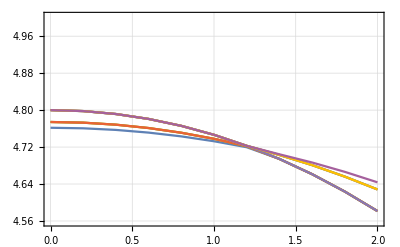

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

1.50178×10^-6

1

0.0000578076

1

0.000226806

1

0.000508737

1

0.000904002

1

0.00141316

1

0.0020369

1

0.0027761

1

0.00363173

1

0.00460491

1

0.00569687

1

0.00690897

1

0.00824263

1

5.93322

1

5.92137

1

5.90836

1

5.89416

1

5.87875

1

5.86211

1

5.84425

1

5.82517

2

2.

2

1.99992

2

1.99969

2

1.99931

2

1.99878

2

1.99809

2

1.99725

2

1.99625

2

1.99509

2

1.99378

2

1.9923

2

1.99065

2

1.98885

2

5.93322

2

5.92137

2

5.90836

2

5.89416

2

5.87875

2

5.86211

2

5.84425

2

5.82517

3

2.

3

1.99992

3

1.99969

3

1.99931

3

1.99878

3

1.99809

3

1.99725

3

1.99625

3

1.99509

3

1.99378

3

1.9923

3

1.99065

3

1.98885

3

5.93322

3

5.92137

3

5.90836

3

5.89416

3

5.87875

3

5.86211

3

5.84425

3

5.82517

4

2.

4

1.99992

4

1.99969

4

1.99931

4

1.99878

4

1.99809

4

1.99725

4

1.99625

4

1.99509

4

1.99378

4

1.9923

4

1.99065

4

1.98885

4

5.93322

4

5.92137

4

5.90836

4

5.89416

4

5.87875

4

5.86211

4

5.84425

4

5.82517

5

6.

5

5.99965

5

5.99859

5

5.99682

5

5.99432

5

5.99106

5

5.98701

5

5.98213

5

5.9764

5

5.96976

5

5.96216

5

5.95357

5

5.94394

5

5.93322

5

5.92137

5

5.90836

5

5.89416

5

5.87875

5

5.86211

5

5.84425

5

5.82517

6

6.

6

5.99965

6

5.99859

6

5.99682

6

5.99432

6

5.99106

6

5.98701

6

5.98213

6

5.9764

6

5.96976

6

5.96216

6

5.95357

6

5.94394

6

0.00969935

6

1.98472

6

1.9824

6

1.97991

6

1.97723

6

1.97438

6

1.97134

6

1.96811

7

6.

7

5.99965

7

5.99859

7

5.99682

7

5.99432

7

5.99106

7

5.98701

7

5.98213

7

5.9764

7

5.96976

7

5.96216

7

5.95357

7

5.94394

7

1.98687

7

1.98472

7

1.9824

7

1.97991

7

1.97723

7

1.97438

7

1.97134

7

1.96811

8

6.

8

5.99965

8

5.99859

8

5.99682

8

5.99432

8

5.99106

8

5.98701

8

5.98213

8

5.9764

8

5.96976

8

5.96216

8

5.95357

8

5.94394

8

1.98687

8

1.98472

8

1.9824

8

1.97991

8

1.97723

8

1.97438

8

1.97134

8

1.96811

9

6.

9

5.99965

9

5.99859

9

5.99682

9

5.99432

9

5.99106

9

5.98701

9

5.98213

9

5.9764

9

5.96976

9

5.96216

9

5.95357

9

5.94394

9

1.98687

9

0.0112807

9

0.0129883

9

0.0148237

9

0.0167887

9

0.0188846

9

0.0211131

9

0.0234756

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

0.744958

10

0.744203

10

0.743407

10

0.742571

10

0.7417

10

0.740796

10

0.739862

10

0.738901

```mathematica
data1//MatrixForm
```

(1 | 0. | 1.50178×10^-6 | 4.76176
1 | 0.1 | 0.0000578076 | 4.76147
1 | 0.2 | 0.000226806 | 4.7606
1 | 0.3 | 0.000508737 | 4.75915
1 | 0.4 | 0.000904002 | 4.75711
1 | 0.5 | 0.00141316 | 4.75449
1 | 0.6 | 0.0020369 | 4.75129
1 | 0.7 | 0.0027761 | 4.7475
1 | 0.8 | 0.00363173 | 4.74312
1 | 0.9 | 0.00460491 | 4.73815
1 | 1. | 0.00569687 | 4.73259
1 | 1.1 | 0.00690897 | 4.72643
1 | 1.2 | 0.00824263 | 4.71967
1 | 1.3 | 5.93322 | 4.70907
1 | 1.4 | 5.92137 | 4.69431
1 | 1.5 | 5.90836 | 4.6784
1 | 1.6 | 5.89416 | 4.66134
1 | 1.7 | 5.87875 | 4.64311
1 | 1.8 | 5.86211 | 4.62372
1 | 1.9 | 5.84425 | 4.60315
1 | 2. | 5.82517 | 4.58142
2 | 0. | 2. | 4.77426
2 | 0.1 | 1.99992 | 4.7739
2 | 0.2 | 1.99969 | 4.77281
2 | 0.3 | 1.99931 | 4.77099
2 | 0.4 | 1.99878 | 4.76845
2 | 0.5 | 1.99809 | 4.76518
2 | 0.6 | 1.99725 | 4.76118
2 | 0.7 | 1.99625 | 4.75645
2 | 0.8 | 1.99509 | 4.75099
2 | 0.9 | 1.99378 | 4.7448
2 | 1. | 1.9923 | 4.73788
2 | 1.1 | 1.99065 | 4.73023
2 | 1.2 | 1.98885 | 4.72185
2 | 1.3 | 5.93322 | 4.70907
2 | 1.4 | 5.92137 | 4.69431
2 | 1.5 | 5.90836 | 4.6784
2 | 1.6 | 5.89416 | 4.66134
2 | 1.7 | 5.87875 | 4.64311
2 | 1.8 | 5.86211 | 4.62372
2 | 1.9 | 5.84425 | 4.60315
2 | 2. | 5.82517 | 4.58142
3 | 0. | 2. | 4.77426
3 | 0.1 | 1.99992 | 4.7739
3 | 0.2 | 1.99969 | 4.77281
3 | 0.3 | 1.99931 | 4.77099
3 | 0.4 | 1.99878 | 4.76845
3 | 0.5 | 1.99809 | 4.76518
3 | 0.6 | 1.99725 | 4.76118
3 | 0.7 | 1.99625 | 4.75645
3 | 0.8 | 1.99509 | 4.75099
3 | 0.9 | 1.99378 | 4.7448
3 | 1. | 1.9923 | 4.73788
3 | 1.1 | 1.99065 | 4.73023
3 | 1.2 | 1.98885 | 4.72185
3 | 1.3 | 5.93322 | 4.70907
3 | 1.4 | 5.92137 | 4.69431
3 | 1.5 | 5.90836 | 4.6784
3 | 1.6 | 5.89416 | 4.66134
3 | 1.7 | 5.87875 | 4.64311
3 | 1.8 | 5.86211 | 4.62372
3 | 1.9 | 5.84425 | 4.60315
3 | 2. | 5.82517 | 4.58142
4 | 0. | 2. | 4.77426
4 | 0.1 | 1.99992 | 4.7739
4 | 0.2 | 1.99969 | 4.77281
4 | 0.3 | 1.99931 | 4.77099
4 | 0.4 | 1.99878 | 4.76845
4 | 0.5 | 1.99809 | 4.76518
4 | 0.6 | 1.99725 | 4.76118
4 | 0.7 | 1.99625 | 4.75645
4 | 0.8 | 1.99509 | 4.75099
4 | 0.9 | 1.99378 | 4.7448
4 | 1. | 1.9923 | 4.73788
4 | 1.1 | 1.99065 | 4.73023
4 | 1.2 | 1.98885 | 4.72185
4 | 1.3 | 5.93322 | 4.70907
4 | 1.4 | 5.92137 | 4.69431
4 | 1.5 | 5.90836 | 4.6784
4 | 1.6 | 5.89416 | 4.66134
4 | 1.7 | 5.87875 | 4.64311
4 | 1.8 | 5.86211 | 4.62372
4 | 1.9 | 5.84425 | 4.60315
4 | 2. | 5.82517 | 4.58142
5 | 0. | 6. | 4.8
5 | 0.1 | 5.99965 | 4.79947
5 | 0.2 | 5.99859 | 4.79788
5 | 0.3 | 5.99682 | 4.79523
5 | 0.4 | 5.99432 | 4.79151
5 | 0.5 | 5.99106 | 4.78673
5 | 0.6 | 5.98701 | 4.78087
5 | 0.7 | 5.98213 | 4.77392
5 | 0.8 | 5.9764 | 4.76589
5 | 0.9 | 5.96976 | 4.75676
5 | 1. | 5.96216 | 4.74652
5 | 1.1 | 5.95357 | 4.73517
5 | 1.2 | 5.94394 | 4.72269
5 | 1.3 | 5.93322 | 4.70907
5 | 1.4 | 5.92137 | 4.69431
5 | 1.5 | 5.90836 | 4.6784
5 | 1.6 | 5.89416 | 4.66134
5 | 1.7 | 5.87875 | 4.64311
5 | 1.8 | 5.86211 | 4.62372
5 | 1.9 | 5.84425 | 4.60315
5 | 2. | 5.82517 | 4.58142
6 | 0. | 6. | 4.8
6 | 0.1 | 5.99965 | 4.79947
6 | 0.2 | 5.99859 | 4.79788
6 | 0.3 | 5.99682 | 4.79523
6 | 0.4 | 5.99432 | 4.79151
6 | 0.5 | 5.99106 | 4.78673
6 | 0.6 | 5.98701 | 4.78087
6 | 0.7 | 5.98213 | 4.77392
6 | 0.8 | 5.9764 | 4.76589
6 | 0.9 | 5.96976 | 4.75676
6 | 1. | 5.96216 | 4.74652
6 | 1.1 | 5.95357 | 4.73517
6 | 1.2 | 5.94394 | 4.72269
6 | 1.3 | 0.00969935 | 4.71232
6 | 1.4 | 1.98472 | 4.70287
6 | 1.5 | 1.9824 | 4.69228
6 | 1.6 | 1.97991 | 4.68096
6 | 1.7 | 1.97723 | 4.66889
6 | 1.8 | 1.97438 | 4.65609
6 | 1.9 | 1.97134 | 4.64254
6 | 2. | 1.96811 | 4.62826
7 | 0. | 6. | 4.8
7 | 0.1 | 5.99965 | 4.79947
7 | 0.2 | 5.99859 | 4.79788
7 | 0.3 | 5.99682 | 4.79523
7 | 0.4 | 5.99432 | 4.79151
7 | 0.5 | 5.99106 | 4.78673
7 | 0.6 | 5.98701 | 4.78087
7 | 0.7 | 5.98213 | 4.77392
7 | 0.8 | 5.9764 | 4.76589
7 | 0.9 | 5.96976 | 4.75676
7 | 1. | 5.96216 | 4.74652
7 | 1.1 | 5.95357 | 4.73517
7 | 1.2 | 5.94394 | 4.72269
7 | 1.3 | 1.98687 | 4.71273
7 | 1.4 | 1.98472 | 4.70287
7 | 1.5 | 1.9824 | 4.69228
7 | 1.6 | 1.97991 | 4.68096
7 | 1.7 | 1.97723 | 4.66889
7 | 1.8 | 1.97438 | 4.65609
7 | 1.9 | 1.97134 | 4.64254
7 | 2. | 1.96811 | 4.62826
8 | 0. | 6. | 4.8
8 | 0.1 | 5.99965 | 4.79947
8 | 0.2 | 5.99859 | 4.79788
8 | 0.3 | 5.99682 | 4.79523
8 | 0.4 | 5.99432 | 4.79151
8 | 0.5 | 5.99106 | 4.78673
8 | 0.6 | 5.98701 | 4.78087
8 | 0.7 | 5.98213 | 4.77392
8 | 0.8 | 5.9764 | 4.76589
8 | 0.9 | 5.96976 | 4.75676
8 | 1. | 5.96216 | 4.74652
8 | 1.1 | 5.95357 | 4.73517
8 | 1.2 | 5.94394 | 4.72269
8 | 1.3 | 1.98687 | 4.71273
8 | 1.4 | 1.98472 | 4.70287
8 | 1.5 | 1.9824 | 4.69228
8 | 1.6 | 1.97991 | 4.68096
8 | 1.7 | 1.97723 | 4.66889
8 | 1.8 | 1.97438 | 4.65609
8 | 1.9 | 1.97134 | 4.64254
8 | 2. | 1.96811 | 4.62826
9 | 0. | 6. | 4.8
9 | 0.1 | 5.99965 | 4.79947
9 | 0.2 | 5.99859 | 4.79788
9 | 0.3 | 5.99682 | 4.79523
9 | 0.4 | 5.99432 | 4.79151
9 | 0.5 | 5.99106 | 4.78673
9 | 0.6 | 5.98701 | 4.78087
9 | 0.7 | 5.98213 | 4.77392
9 | 0.8 | 5.9764 | 4.76589
9 | 0.9 | 5.96976 | 4.75676
9 | 1. | 5.96216 | 4.74652
9 | 1.1 | 5.95357 | 4.73517
9 | 1.2 | 5.94394 | 4.72269
9 | 1.3 | 1.98687 | 4.71273
9 | 1.4 | 0.0112807 | 4.70435
9 | 1.5 | 0.0129883 | 4.69578
9 | 1.6 | 0.0148237 | 4.6866
9 | 1.7 | 0.0167887 | 4.6768
9 | 1.8 | 0.0188846 | 4.66638
9 | 1.9 | 0.0211131 | 4.65534
9 | 2. | 0.0234756 | 4.64367
10 | 0. | 3.75 | 5.65836
10 | 0.1 | 3.75 | 5.65836
10 | 0.2 | 3.75 | 5.65836
10 | 0.3 | 3.75 | 5.65836
10 | 0.4 | 3.75 | 5.65836
10 | 0.5 | 3.75 | 5.65836
10 | 0.6 | 3.75 | 5.65836
10 | 0.7 | 3.75 | 5.65836
10 | 0.8 | 3.75 | 5.65836
10 | 0.9 | 3.75 | 5.65836
10 | 1. | 3.75 | 5.65836
10 | 1.1 | 3.75 | 5.65836
10 | 1.2 | 3.75 | 5.65836
10 | 1.3 | 0.744958 | 5.65518
10 | 1.4 | 0.744203 | 5.64066
10 | 1.5 | 0.743407 | 5.62509
10 | 1.6 | 0.742571 | 5.60848
10 | 1.7 | 0.7417 | 5.59082
10 | 1.8 | 0.740796 | 5.57213
10 | 1.9 | 0.739862 | 5.55241
10 | 2. | 0.738901 | 5.53167)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;13,1;;4]];
tmp02 = data1[[119;;119,1;;4]];
tmp03 = data1[[183;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;34,1;;4]];
tmp02 = data1[[140;;147, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 4.76176 | 1.50178×10^-6
0.1 | 4.76147 | 0.0000578076
0.2 | 4.7606 | 0.000226806
0.3 | 4.75915 | 0.000508737
0.4 | 4.75711 | 0.000904002
0.5 | 4.75449 | 0.00141316
0.6 | 4.75129 | 0.0020369
0.7 | 4.7475 | 0.0027761
0.8 | 4.74312 | 0.00363173
0.9 | 4.73815 | 0.00460491
1. | 4.73259 | 0.00569687
1.1 | 4.72643 | 0.00690897
1.2 | 4.71967 | 0.00824263
1.3 | 4.71232 | 0.00969935
1.4 | 4.70435 | 0.0112807
1.5 | 4.69578 | 0.0129883
1.6 | 4.6866 | 0.0148237
1.7 | 4.6768 | 0.0167887
1.8 | 4.66638 | 0.0188846
1.9 | 4.65534 | 0.0211131
2. | 4.64367 | 0.0234756)

(0. | 4.77426 | 2.
0.1 | 4.7739 | 1.99992
0.2 | 4.77281 | 1.99969
0.3 | 4.77099 | 1.99931
0.4 | 4.76845 | 1.99878
0.5 | 4.76518 | 1.99809
0.6 | 4.76118 | 1.99725
0.7 | 4.75645 | 1.99625
0.8 | 4.75099 | 1.99509
0.9 | 4.7448 | 1.99378
1. | 4.73788 | 1.9923
1.1 | 4.73023 | 1.99065
1.2 | 4.72185 | 1.98885
1.3 | 4.71273 | 1.98687
1.4 | 4.70287 | 1.98472
1.5 | 4.69228 | 1.9824
1.6 | 4.68096 | 1.97991
1.7 | 4.66889 | 1.97723
1.8 | 4.65609 | 1.97438
1.9 | 4.64254 | 1.97134
2. | 4.62826 | 1.96811)

(0. | 4.8 | 6.
0.1 | 4.79947 | 5.99965
0.2 | 4.79788 | 5.99859
0.3 | 4.79523 | 5.99682
0.4 | 4.79151 | 5.99432
0.5 | 4.78673 | 5.99106
0.6 | 4.78087 | 5.98701
0.7 | 4.77392 | 5.98213
0.8 | 4.76589 | 5.9764
0.9 | 4.75676 | 5.96976
1. | 4.74652 | 5.96216
1.1 | 4.73517 | 5.95357
1.2 | 4.72269 | 5.94394
1.3 | 4.70907 | 5.93322
1.4 | 4.69431 | 5.92137
1.5 | 4.6784 | 5.90836
1.6 | 4.66134 | 5.89416
1.7 | 4.64311 | 5.87875
1.8 | 4.62372 | 5.86211
1.9 | 4.60315 | 5.84425
2. | 4.58142 | 5.82517)

```mathematica
|
```

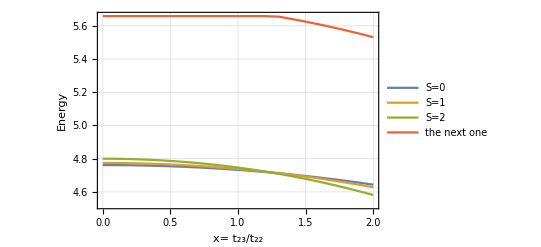

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

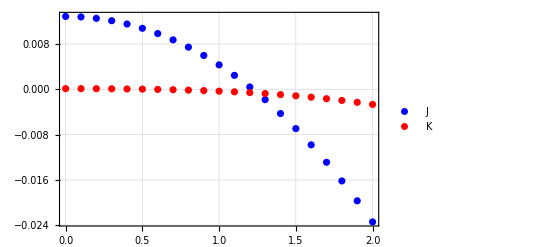

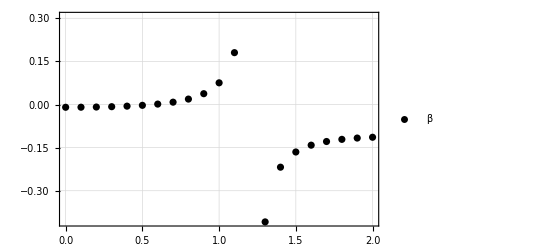

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```